Here we collect the plots in “EscapeTimeScatteringFunction2.nb”

```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\EscapeTimeScatteringFunction\NewZoomRegions

```mathematica
SetAttributes[swap,HoldFirst];
```

```mathematica
swap[list_,a_,b_]:={list[[a]],list[[b]]}={list[[b]],list[[a]]};
```

## Positive l (ε=ε_crit+0.2)

```mathematica
files1=FileNames["pl_b(01)_e(12)_phi*"]
```

{pl_b(01)_e(12)_phi(1_2).mx,pl_b(01)_e(12)_phi(15_17).mx,pl_b(01)_e(12)_phi(157_158).mx,pl_b(01)_e(12)_phi(-225_-223).mx,pl_b(01)_e(12)_phi(-24_-22).mx,pl_b(01)_e(12)_phi(-3_-2).mx}

```mathematica
swap[files1,4,6];files1
```

{pl_b(01)_e(12)_phi(1_2).mx,pl_b(01)_e(12)_phi(15_17).mx,pl_b(01)_e(12)_phi(157_158).mx,pl_b(01)_e(12)_phi(-3_-2).mx,pl_b(01)_e(12)_phi(-24_-22).mx,pl_b(01)_e(12)_phi(-225_-223).mx}

```mathematica
datab01=Import[#]&/@files1;
```

```mathematica
files2=FileNames["pl_b(05)_e(12)_phi*"]
```

{pl_b(05)_e(12)_phi(1_2).mx,pl_b(05)_e(12)_phi(15_17).mx,pl_b(05)_e(12)_phi(157_158).mx,pl_b(05)_e(12)_phi(-225_-223).mx,pl_b(05)_e(12)_phi(-24_-22).mx,pl_b(05)_e(12)_phi(-3_-2).mx}

```mathematica
swap[files2,4,6];files2
```

{pl_b(05)_e(12)_phi(1_2).mx,pl_b(05)_e(12)_phi(15_17).mx,pl_b(05)_e(12)_phi(157_158).mx,pl_b(05)_e(12)_phi(-3_-2).mx,pl_b(05)_e(12)_phi(-24_-22).mx,pl_b(05)_e(12)_phi(-225_-223).mx}

```mathematica
datab05=Import[#]&/@files2;
```

```mathematica
plot=Table[ListPlot[{datab01⟦i⟧,datab05⟦i⟧},PlotRange->{All,{0,10000}},AxesLabel->{"ϕ_sh","T_e"},PlotStyle->{{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},PlotLegends-> Placed[LineLegend[{Blue,Red},{"b=0.1","b=0.5"},Joined->{True,True},LegendMarkerSize->80],{Right,Top}]],{i,1,6}];
```

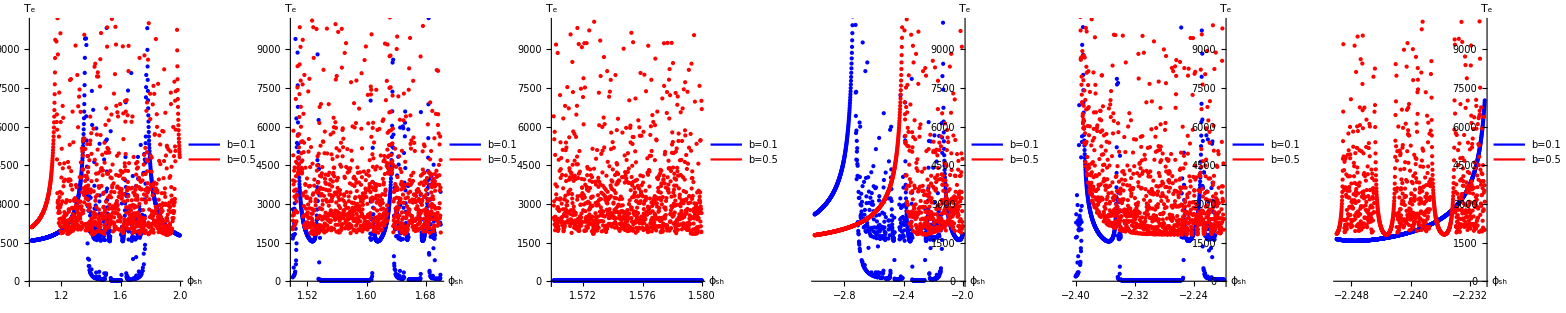

```mathematica
{Array[Show[plot⟦#⟧,ImageSize->800]&,6]}//Grid
```

```mathematica
Table[Export["plNearCritE"<>ToString[i]<>".png",Show[plot⟦i⟧,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]],{i,1,6}];
```

## Positive l (ε=ε_crit+2)

```mathematica
files1=FileNames["pl_b(01)_e(30)_phi*"]
```

{pl_b(01)_e(30)_phi(12_18).mx,pl_b(01)_e(30)_phi(140_150).mx,pl_b(01)_e(30)_phi(152_162).mx,pl_b(01)_e(30)_phi(-232_-224).mx,pl_b(01)_e(30)_phi(-26_-22).mx}

```mathematica
swap[files1,4,5];files1
```

{pl_b(01)_e(30)_phi(12_18).mx,pl_b(01)_e(30)_phi(140_150).mx,pl_b(01)_e(30)_phi(152_162).mx,pl_b(01)_e(30)_phi(-26_-22).mx,pl_b(01)_e(30)_phi(-232_-224).mx}

```mathematica
datab01=Import[#]&/@files1;
```

```mathematica
files2=FileNames["pl_b(05)_e(30)_phi*"]
```

{pl_b(05)_e(30)_phi(12_18).mx,pl_b(05)_e(30)_phi(140_150).mx,pl_b(05)_e(30)_phi(152_162).mx,pl_b(05)_e(30)_phi(-232_-224).mx,pl_b(05)_e(30)_phi(-26_-22).mx}

```mathematica
swap[files2,4,5];files2
```

{pl_b(05)_e(30)_phi(12_18).mx,pl_b(05)_e(30)_phi(140_150).mx,pl_b(05)_e(30)_phi(152_162).mx,pl_b(05)_e(30)_phi(-26_-22).mx,pl_b(05)_e(30)_phi(-232_-224).mx}

```mathematica
datab05=Import[#]&/@files2;
```

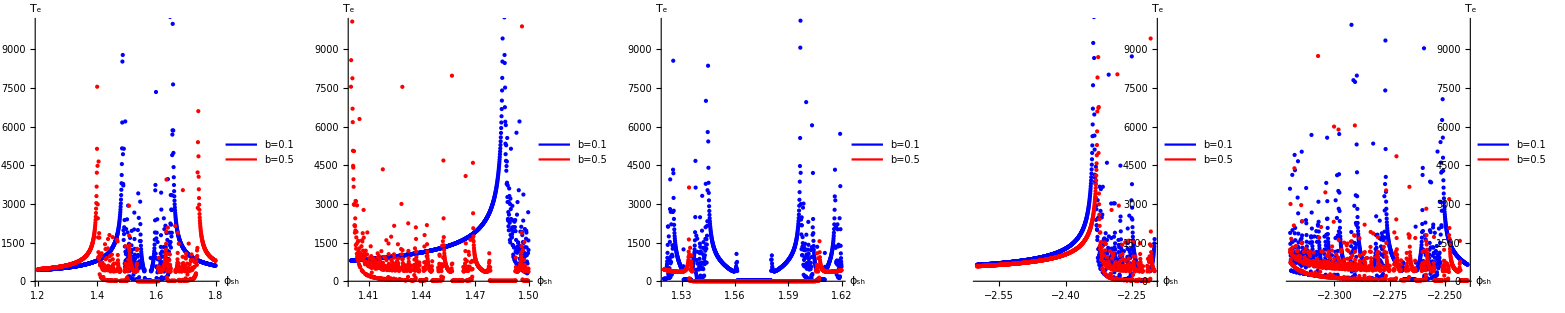

```mathematica
numPlots=Length[datab01];plot=Table[ListPlot[{datab01⟦i⟧,datab05⟦i⟧},PlotRange->{All,{0,10000}},AxesLabel->{"ϕ_sh","T_e"},PlotStyle->{{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},PlotLegends-> Placed[LineLegend[{Blue,Red},{"b=0.1","b=0.5"},Joined->{True,True},LegendMarkerSize->80],{Right,Top}]],{i,1,numPlots}];
{Array[Show[plot⟦#⟧,ImageSize->800]&,numPlots]}//Grid
```

```mathematica
Table[Export["plFarCritE"<>ToString[i]<>".png",Show[plot⟦i⟧,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]],{i,1,numPlots}];
```

## Negative l (ε=ε_crit+0.2)

```mathematica
files1=FileNames["ml_b(001)_e(crit_02)_phi*"]
```

{ml_b(001)_e(crit_02)_phi(1_2).mx,ml_b(001)_e(crit_02)_phi(15_165).mx,ml_b(001)_e(crit_02)_phi(-27_-255).mx,ml_b(001)_e(crit_02)_phi(-3_-2).mx}

```mathematica
swap[files1,3,4];files1
```

{ml_b(001)_e(crit_02)_phi(1_2).mx,ml_b(001)_e(crit_02)_phi(15_165).mx,ml_b(001)_e(crit_02)_phi(-3_-2).mx,ml_b(001)_e(crit_02)_phi(-27_-255).mx}

```mathematica
datab001=Import[#]&/@files1;
```

```mathematica
files2=FileNames["ml_b(01)_e(crit_02)_phi*"]
```

{ml_b(01)_e(crit_02)_phi(1_2).mx,ml_b(01)_e(crit_02)_phi(15_165).mx,ml_b(01)_e(crit_02)_phi(-27_-255).mx,ml_b(01)_e(crit_02)_phi(-3_-2).mx}

```mathematica
swap[files2,3,4];files2
```

{ml_b(01)_e(crit_02)_phi(1_2).mx,ml_b(01)_e(crit_02)_phi(15_165).mx,ml_b(01)_e(crit_02)_phi(-3_-2).mx,ml_b(01)_e(crit_02)_phi(-27_-255).mx}

```mathematica
datab01=Import[#]&/@files2;
```

```mathematica
files3=FileNames["ml_b(05)_e(crit_02)_phi*"]
```

{ml_b(05)_e(crit_02)_phi(1_2).mx,ml_b(05)_e(crit_02)_phi(15_165).mx,ml_b(05)_e(crit_02)_phi(-27_-255).mx,ml_b(05)_e(crit_02)_phi(-3_-2).mx}

```mathematica
swap[files3,3,4];files3
```

{ml_b(05)_e(crit_02)_phi(1_2).mx,ml_b(05)_e(crit_02)_phi(15_165).mx,ml_b(05)_e(crit_02)_phi(-3_-2).mx,ml_b(05)_e(crit_02)_phi(-27_-255).mx}

```mathematica
datab05=Import[#]&/@files3;
```

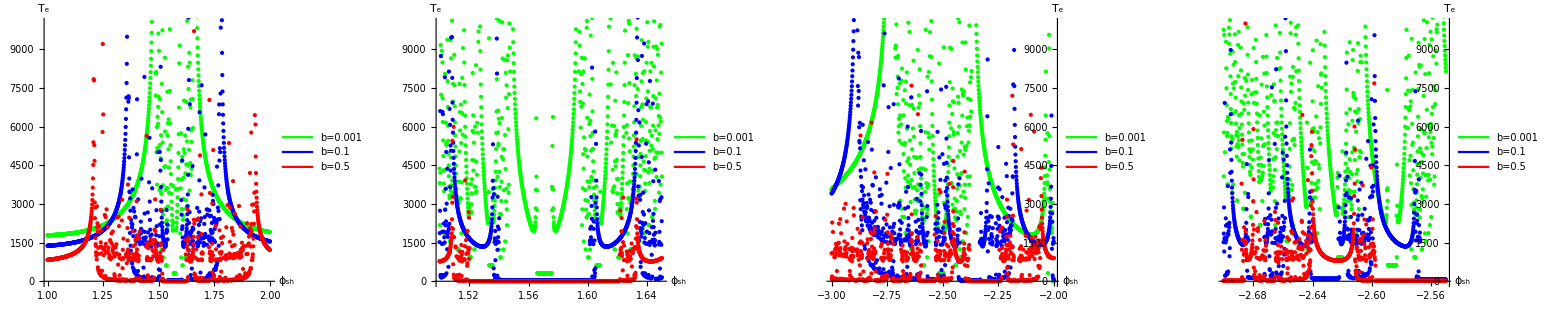

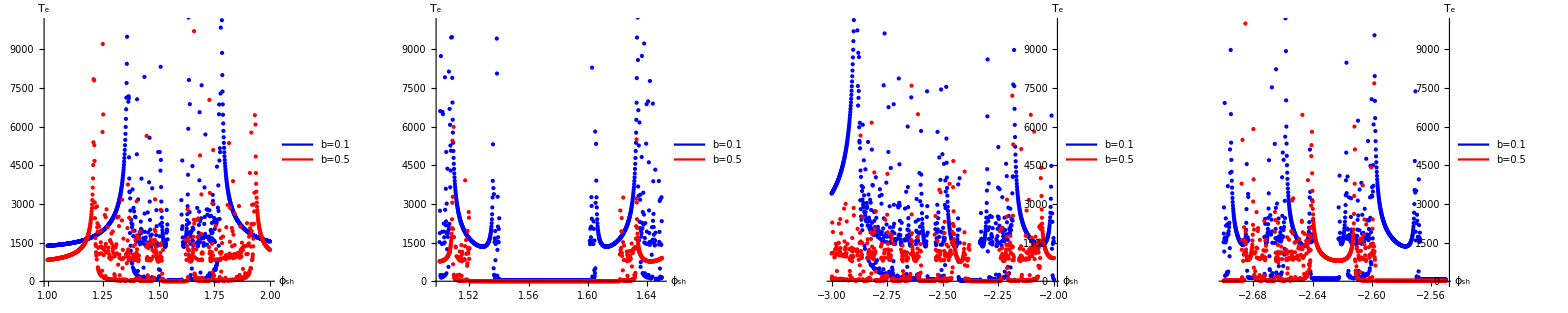

```mathematica
numPlots=Length[datab01];plotw001=Table[ListPlot[{datab001⟦i⟧,datab01⟦i⟧,datab05⟦i⟧},PlotRange->{All,{0,10000}},AxesLabel->{"ϕ_sh","T_e"},PlotStyle->{{Green,PointSize[Medium]},{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},PlotLegends-> Placed[LineLegend[{Green,Blue,Red},{"b=0.001","b=0.1","b=0.5"},Joined->{True,True,True},LegendMarkerSize->80],{Right,Top}]],{i,1,numPlots}];
plotwo001=Table[ListPlot[{datab01⟦i⟧,datab05⟦i⟧},PlotRange->{All,{0,10000}},AxesLabel->{"ϕ_sh","T_e"},PlotStyle->{{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},PlotLegends-> Placed[LineLegend[{Blue,Red},{"b=0.1","b=0.5"},Joined->{True,True},LegendMarkerSize->80],{Right,Top}]],{i,1,numPlots}];
{Array[Show[plotw001⟦#⟧,ImageSize->800]&,numPlots]}//Grid
{Array[Show[plotwo001⟦#⟧,ImageSize->800]&,numPlots]}//Grid
```

```mathematica
Table[Export["mlNearCritE(wo001)"<>ToString[i]<>".png",Show[plotwo001⟦i⟧,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]],{i,1,numPlots}];
Table[Export["mlNearCritE(w001)"<>ToString[i]<>".png",Show[plotw001⟦i⟧,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]],{i,1,numPlots}];
```

## Negative l (ε=ε_crit+2)

```mathematica
files1=FileNames["ml_b(001)_e(crit_2)_phi*"]
```

{ml_b(001)_e(crit_2)_phi(12_2).mx,ml_b(001)_e(crit_2)_phi(15_165).mx,ml_b(001)_e(crit_2)_phi(-23_-22).mx,ml_b(001)_e(crit_2)_phi(-28_-2).mx}

```mathematica
swap[files1,3,4];files1
```

{ml_b(001)_e(crit_2)_phi(12_2).mx,ml_b(001)_e(crit_2)_phi(15_165).mx,ml_b(001)_e(crit_2)_phi(-28_-2).mx,ml_b(001)_e(crit_2)_phi(-23_-22).mx}

```mathematica
datab001=Import[#]&/@files1;
```

```mathematica
files2=FileNames["ml_b(01)_e(crit_2)_phi*"]
```

{ml_b(01)_e(crit_2)_phi(12_2).mx,ml_b(01)_e(crit_2)_phi(15_165).mx,ml_b(01)_e(crit_2)_phi(-23_-22).mx,ml_b(01)_e(crit_2)_phi(-28_-2).mx}

```mathematica
swap[files2,3,4];files2
```

{ml_b(01)_e(crit_2)_phi(12_2).mx,ml_b(01)_e(crit_2)_phi(15_165).mx,ml_b(01)_e(crit_2)_phi(-28_-2).mx,ml_b(01)_e(crit_2)_phi(-23_-22).mx}

```mathematica
datab01=Import[#]&/@files2;
```

```mathematica
files3=FileNames["ml_b(05)_e(crit_2)_phi*"]
```

{ml_b(05)_e(crit_2)_phi(12_2).mx,ml_b(05)_e(crit_2)_phi(15_165).mx,ml_b(05)_e(crit_2)_phi(-23_-22).mx,ml_b(05)_e(crit_2)_phi(-28_-2).mx}

```mathematica
swap[files3,3,4];files3
```

{ml_b(05)_e(crit_2)_phi(12_2).mx,ml_b(05)_e(crit_2)_phi(15_165).mx,ml_b(05)_e(crit_2)_phi(-28_-2).mx,ml_b(05)_e(crit_2)_phi(-23_-22).mx}

```mathematica
datab05=Import[#]&/@files3;
```

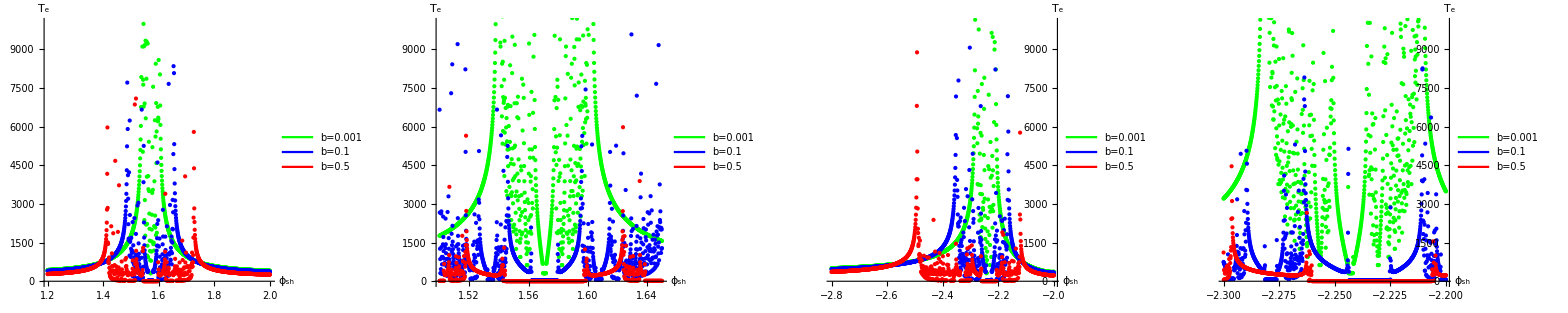

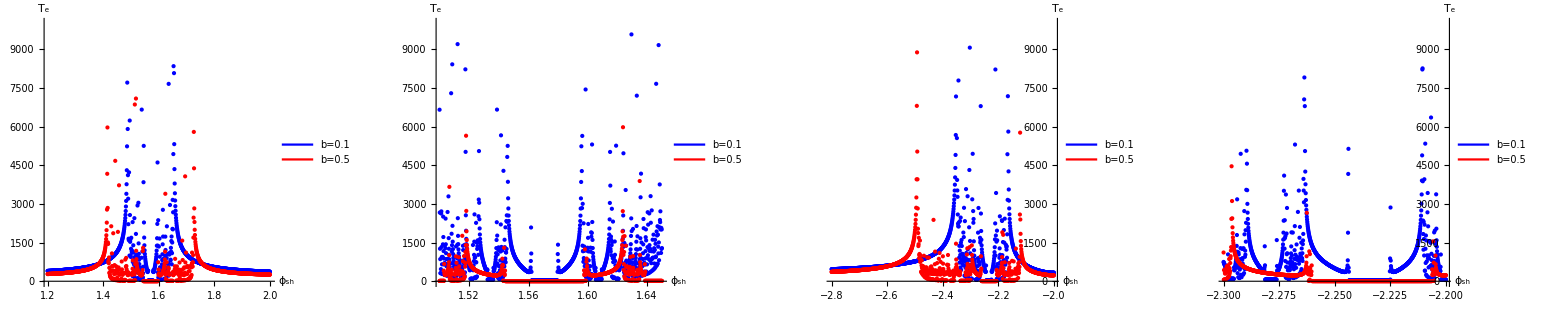

```mathematica
numPlots=Length[datab01];plotw001=Table[ListPlot[{datab001⟦i⟧,datab01⟦i⟧,datab05⟦i⟧},PlotRange->{All,{0,10000}},AxesLabel->{"ϕ_sh","T_e"},PlotStyle->{{Green,PointSize[Medium]},{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},PlotLegends-> Placed[LineLegend[{Green,Blue,Red},{"b=0.001","b=0.1","b=0.5"},Joined->{True,True,True},LegendMarkerSize->80],{Right,Top}]],{i,1,numPlots}];
plotwo001=Table[ListPlot[{datab01⟦i⟧,datab05⟦i⟧},PlotRange->{All,{0,10000}},AxesLabel->{"ϕ_sh","T_e"},PlotStyle->{{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},PlotLegends-> Placed[LineLegend[{Blue,Red},{"b=0.1","b=0.5"},Joined->{True,True},LegendMarkerSize->80],{Right,Top}]],{i,1,numPlots}];
{Array[Show[plotw001⟦#⟧,ImageSize->800]&,numPlots]}//Grid
{Array[Show[plotwo001⟦#⟧,ImageSize->800]&,numPlots]}//Grid
```

```mathematica
Table[Export["mlFarCritE(wo001)"<>ToString[i]<>".png",Show[plotwo001⟦i⟧,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]],{i,1,numPlots}];
Table[Export["mlFarCritE(w001)"<>ToString[i]<>".png",Show[plotw001⟦i⟧,ImageSize->2000,BaseStyle->{FontSize->40},LabelStyle->{FontSize->40}]],{i,1,numPlots}];
```